```mathematica
beta=4.0/Pi
phi0=0.90
xi=0.2
coeff=3.0/2.0
```

1.27324

0.9

0.2

1.5

```mathematica
extBrady[pea_,peb_,xa_,phi_]:=((((pea^2)*xa)+((peb^2)*(1.0-xa)))*(1.0-(2.0*phi)-(3.0*xi*(phi^2))))+((coeff)*((pea*xa)+(peb*(1.0-xa)))*(beta*((2.0*phi*((1.0-(phi/phi0))^-1))+(((phi^2)/phi)*((1.0-(phi/phi0))^-2)))))
```

```mathematica
Solve[extBrady[20,100,xa,0.6]==0,xa]
```

{{xa→0.932261}}

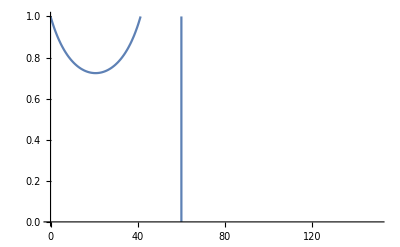

```mathematica
Plot[xa /. Solve[extBrady[pea, 60,xa,0.6]==0, xa], {pea, 0,150}, PlotRange->{{0,150},{0,1}}]
```

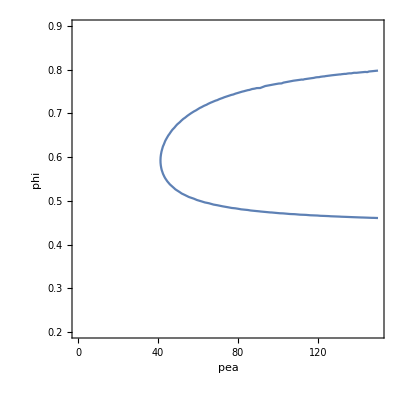

```mathematica
ContourPlot[extBrady[pea, 0,1.0,phi]==0,{pea,0,150},{phi,0.2,0.9}, AxesLabel->Automatic]
```

```mathematica
ContourPlot3D[extBrady[pea, peb,xa,0.6]==0,{pea,0,150},{peb,0,150},{xa,0,1},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
(* I am going to try weighting the average of the result instead *)
```

```mathematica
phiTot=0.6
```

0.6

```mathematica
monoSpinodal[pea_]:=1-(2*phiTot)-(3*xi*(phiTot^2))+(beta*pea*(2*phiTot*((1-(phiTot/phi0))^-1)+((phiTot^2)/phi0)*((1-(phiTot/phi0))^-2)))
```

```mathematica
binarySpinodal[pea_,peb_,xa_]:=(monoSpinodal[pea]*xa)+(monoSpinodal[peb]*(1-xa))
```

```mathematica
ContourPlot3D[binarySpinodal[pea, peb,xa],{pea,0,150},{peb,0,150},{xa,0,1},AxesLabel->Automatic,PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
beta=4/Pi
xi=0.2
phi0=0.90
```

4/π

0.2

0.9

```mathematica
(* Let's try to do the derived method again *)
derivedBinSpin[phi_,pera_,perb_,xa_]:=((pera)^-2)*
(1-(2*phi)-(3*xi*(phi^2))+(beta*pera)*
(
(2*phi)*((1-(phi/phi0))^-1)+((phi/phi0)*((1-(phi/phi0))^-2))
))*xa+
((perb)^-2)*
(1-(2*phi)-(3*xi*(phi^2))+(beta*perb)*
(
(2*phi)*((1-(phi/phi0))^-1)+((phi/phi0)*((1-(phi/phi0))^-2))
))*(1-xa)
```

```mathematica
(* per=((pe^-1)*(3/2)) *)
```

```mathematica
derivedBinSpinPE[phi_,pea_,peb_,xa_]:=((((pea^-1)*(3/2)))^-2)*
(1-(2*phi)-(3*xi*(phi^2))+(beta*((pea^-1)*(3/2)))*
(
(2*phi)*((1-(phi/phi0))^-1)+((phi/phi0)*((1-(phi/phi0))^-2))
))*xa+
((((peb^-1)*(3/2)))^-2)*
(1-(2*phi)-(3*xi*(phi^2))+(beta*((peb^-1)*(3/2)))*
(
(2*phi)*((1-(phi/phi0))^-1)+((phi/phi0)*((1-(phi/phi0))^-2))
))*(1-xa)
```

```mathematica
ContourPlot3D[derivedBinSpinPE[0.6,pea,peb,xa]==0,{pea,0,150},{peb,0,150},{xa,0,1}]
```

-Graphics3D-

```mathematica
(* What does it look like if we just compute the pressure? *)
```